# ROBOT PARALELO 3RRR PROGRAMA 3. APROXIMACIÓN A LA CINEMÁTICA DIRECTA POR MTH Y SIMULACIÓN POR CINEMÁTICA INVERSA MÉTODO NUMÉRICO.

Se obtienen las ecuaciones de cinemática directa a partir de la tabla de Denavit-Hartenberg, así como se validan utilizando el método numérico de Newton Raphson.

## FUNCIONES

```mathematica
(*FUNCIONES DE Matrices de Rotación 3x3 PARA CUALQUIER VARIABLE *)
Rx[α_]:={{1,0,0},{0,Cos[α], -Sin[α]}, {0,Sin[α], Cos[α]}};   
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0}, {-Sin[ϕ],0,Cos[ϕ]}};  
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}};
(*FUNCIONES de Matrices HOMEGENEAS de Traslación y Rotación 4x4 PARA CUALQUIER VARIABLE *)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}
Txyz[x_,y_,z_]:=Tx[x].Ty[y].Tz[z]
Qx[α_]:={{1,0,0,0},{0,Cos[α], -Sin[α], 0},{0, Sin[α], Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ], 0, Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ], -Sin[θ],0,0},{Sin[θ], Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
(*FUNCIONES de Matrices HOMEGENEAS De Denavit-Hartenberg *)
Q[θ_, d_, a_, α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]
Ma=Q[θ1, d1, a1, α1];
Ma//MatrixForm
(*FUNCIONES ADICIONALES *)
n={0,0,0,1};
T3D[P_]:={P⟦1⟧,P⟦2⟧,P⟦3⟧ }
M3D[Q_]:={{Q⟦1,1⟧,Q⟦1,2⟧, Q⟦1,3⟧ },{Q⟦2,1⟧,Q⟦2,2⟧, Q⟦2,3⟧},{Q⟦3,1⟧,Q⟦3,2⟧, Q⟦3,3⟧}}
T={{NX, OX, AX},{NY, OY, AY},{NZ, OZ, AZ}};
T//MatrixForm
(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

(Cos[θ1] | -Cos[α1] Sin[θ1] | Sin[α1] Sin[θ1] | a1 Cos[θ1]
Sin[θ1] | Cos[α1] Cos[θ1] | -Cos[θ1] Sin[α1] | a1 Sin[θ1]
0 | Sin[α1] | Cos[α1] | d1
0 | 0 | 0 | 1)

(NX | OX | AX
NY | OY | AY
NZ | OZ | AZ)

## CINEMÁTICA DIRECTA 5 GDL DENAVIT-HARTENBERG

## MTH7- OBTENER LAS MATRICES ^(i-1)A_i

```mathematica
(*Cadena 1 *)
Underoverscript[a, 11, 0]=Qz[θ11].Tx[ℓ11];
Underoverscript[a, 12, 11]=Qz[θ12].Tx[ℓ12];
Underoverscript[a, 13, 12]=Qz[θ13].Tx[ℓ13];
(*Cadena 2*)
Underoverscript[a, 20, 0]=Txyz[ℓx2,ℓy2,0];
Underoverscript[a, 21, 20]=Qz[θ21].Tx[ℓ21];
Underoverscript[a, 22, 21]=Qz[θ22].Tx[ℓ22];
Underoverscript[a, 23, 22]=Qz[θ23].Tx[ℓ23];
(*Cadena 3*)
Underoverscript[a, 30, 0]=Txyz[ℓx3,ℓy3,0];
Underoverscript[a, 31, 30]=Qz[θ31].Tx[ℓ31];
Underoverscript[a, 32, 31]=Qz[θ32].Tx[ℓ32];
Underoverscript[a, 33, 32]=Qz[θ33].Tx[ℓ33];
```

## MTH8- OBTENER LAS MATRICES ^0 A_5=^0 A_1.^1 A_2.^2 A_3.....

```mathematica
(*Cadena 1*)
Underoverscript[a, 12, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11]//Simplify;
Underoverscript[a, 13, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11].Underoverscript[a, 13, 12]//Simplify;
Underoverscript[a, 13, 0].n//MatrixForm

(*Cadena 2*)
Underoverscript[a, 21, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20]//Simplify;
Underoverscript[a, 22, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20].Underoverscript[a, 22, 21]//Simplify;
Underoverscript[a, 23, 0]=Underoverscript[a, 20, 0].Underoverscript[a, 21, 20].Underoverscript[a, 22, 21].Underoverscript[a, 23, 22]//Simplify;
Underoverscript[a, 23, 0].n//MatrixForm

(*Cadena 3*)
Underoverscript[a, 31, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30]//Simplify;
Underoverscript[a, 32, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30].Underoverscript[a, 32, 31]//Simplify;
Underoverscript[a, 33, 0]=Underoverscript[a, 30, 0].Underoverscript[a, 31, 30].Underoverscript[a, 32, 31].Underoverscript[a, 33, 32]//Simplify;
Underoverscript[a, 33, 0].n//MatrixForm
```

(ℓ11 Cos[θ11]+ℓ12 Cos[θ11+θ12]+ℓ13 Cos[θ11+θ12+θ13]
ℓ11 Sin[θ11]+ℓ12 Sin[θ11+θ12]+ℓ13 Sin[θ11+θ12+θ13]
0
1)

(ℓx2+ℓ21 Cos[θ21]+ℓ22 Cos[θ21+θ22]+ℓ23 Cos[θ21+θ22+θ23]
ℓy2+ℓ21 Sin[θ21]+ℓ22 Sin[θ21+θ22]+ℓ23 Sin[θ21+θ22+θ23]
0
1)

(ℓx3+ℓ31 Cos[θ31]+ℓ32 Cos[θ31+θ32]+ℓ33 Cos[θ31+θ32+θ33]
ℓy3+ℓ31 Sin[θ31]+ℓ32 Sin[θ31+θ32]+ℓ33 Sin[θ31+θ32+θ33]
0
1)

## MTH9- Vector de Posición del Efector Final y SubMatriz de Orientación

### Vector de Posición

```mathematica
(*CADENA 1 *)
X1=Underoverscript[a, 13, 0]⟦1,4⟧//Simplify
Y1=Underoverscript[a, 13, 0]⟦2,4⟧//Simplify
Z1=Underoverscript[a, 13, 0]⟦3,4⟧//Simplify;
Φ1=θ11+θ12+θ13-30°

(*CADENA 2*)
X2=Underoverscript[a, 23, 0]⟦1,4⟧//Simplify
Y2=Underoverscript[a, 23, 0]⟦2,4⟧//Simplify
Z2=Underoverscript[a, 23, 0]⟦3,4⟧//Simplify;
Φ2=θ21+θ22+θ23-150°

(*CADENA 3*)
X3=Underoverscript[a, 33, 0]⟦1,4⟧//Simplify
Y3=Underoverscript[a, 33, 0]⟦2,4⟧//Simplify
Z3=Underoverscript[a, 33, 0]⟦3,4⟧//Simplify;
Φ3=θ31+θ32+θ33-270°
```

ℓ11 Cos[θ11]+ℓ12 Cos[θ11+θ12]+ℓ13 Cos[θ11+θ12+θ13]

ℓ11 Sin[θ11]+ℓ12 Sin[θ11+θ12]+ℓ13 Sin[θ11+θ12+θ13]

-30 °+θ11+θ12+θ13

ℓx2+ℓ21 Cos[θ21]+ℓ22 Cos[θ21+θ22]+ℓ23 Cos[θ21+θ22+θ23]

ℓy2+ℓ21 Sin[θ21]+ℓ22 Sin[θ21+θ22]+ℓ23 Sin[θ21+θ22+θ23]

-150 °+θ21+θ22+θ23

ℓx3+ℓ31 Cos[θ31]+ℓ32 Cos[θ31+θ32]+ℓ33 Cos[θ31+θ32+θ33]

ℓy3+ℓ31 Sin[θ31]+ℓ32 Sin[θ31+θ32]+ℓ33 Sin[θ31+θ32+θ33]

-270 °+θ31+θ32+θ33

### SubMatriz de Rotación (ORIENTACIÓN DEL EFECTOR FINAL)

```mathematica
(*CADENA 1*)
NX1=Underoverscript[a, 13, 0]⟦1,1⟧//FullSimplify;
OX1=Underoverscript[a, 13, 0]⟦1,2⟧//FullSimplify;
AX1=Underoverscript[a, 13, 0]⟦1,3⟧//FullSimplify;

NY1=Underoverscript[a, 13, 0]⟦2,1⟧//FullSimplify;
OY1=Underoverscript[a, 13, 0]⟦2,2⟧//FullSimplify;
AY1=Underoverscript[a, 13, 0]⟦2,3⟧//FullSimplify;

NZ1=Underoverscript[a, 13, 0]⟦3,1⟧//FullSimplify;
OZ1=Underoverscript[a, 13, 0]⟦3,2⟧//FullSimplify;
AZ1=Underoverscript[a, 13, 0]⟦3,3⟧//FullSimplify;
(*CADENA 2*)
NX2=Underoverscript[a, 23, 0]⟦1,1⟧//FullSimplify;
OX2=Underoverscript[a, 23, 0]⟦1,2⟧//FullSimplify;
AX2=Underoverscript[a, 23, 0]⟦1,3⟧//FullSimplify;

NY2=Underoverscript[a, 23, 0]⟦2,1⟧//FullSimplify;
OY2=Underoverscript[a, 23, 0]⟦2,2⟧//FullSimplify;
AY2=Underoverscript[a, 23, 0]⟦2,3⟧//FullSimplify;

NZ2=Underoverscript[a, 23, 0]⟦3,1⟧//FullSimplify;
OZ2=Underoverscript[a, 23, 0]⟦3,2⟧//FullSimplify;
AZ2=Underoverscript[a, 23, 0]⟦3,3⟧//FullSimplify;

(*CADENA 3*)
NX3=Underoverscript[a, 33, 0]⟦1,1⟧//FullSimplify;
OX3=Underoverscript[a, 33, 0]⟦1,2⟧//FullSimplify;
AX3=Underoverscript[a, 33, 0]⟦1,3⟧//FullSimplify;

NY3=Underoverscript[a, 33, 0]⟦2,1⟧//FullSimplify;
OY3=Underoverscript[a, 33, 0]⟦2,2⟧//FullSimplify;
AY3=Underoverscript[a, 33, 0]⟦2,3⟧//FullSimplify;

NZ3=Underoverscript[a, 33, 0]⟦3,1⟧//FullSimplify;
OZ3=Underoverscript[a, 33, 0]⟦3,2⟧//FullSimplify;
AZ3=Underoverscript[a, 33, 0]⟦3,3⟧//FullSimplify;
```

## CINEMÁTICA IVERSA POR NEWTON-RAPHSON

### DATOS

```mathematica
ℓ11=30;
ℓ12=40;
ℓ13=15;

ℓ21=30;
ℓ22=40;
ℓ23=15;

ℓ31=30;
ℓ32=40;
ℓ33=15;

ℓx2=60;
ℓy2=0;
ℓx3=30;
ℓy3=60;
 

ϕ=10°;

P1={50,50,0};
P2={40,30,0};
tf=20;

Cero={0,0,0};
(*Método numerico necesita valores iniciales de las variables articulares, para realizar las iteraciones, *)
θ11i=20°;
θ12i=45°;
θ13i=20°;

θ21i=20°;
θ22i=45°;
θ23i=20°;

θ31i=20°;
θ32i=45°;
θ33i=20°;
(*MÉTODO NÚMERICO DE N-R*)
For[t=0, t≤tf, t+=1,
LineaRecta=P1+(t/tf)*(P2-P1);
x[t]=LineaRecta⟦1⟧;
y[t]=LineaRecta⟦2⟧;
z[t]=LineaRecta⟦3⟧;
(*Resolver el sistema de ecuaciones 3 ecuaciones 3 incógnitas*)
(*CADENA 1*)
VartArt1[t]=FindRoot[
{X1==x[t], Y1==y[t], Φ1==ϕ},{θ11,θ11i},{θ12,θ12i},{θ13,θ13i},MaxIterations->50];
θ11i=θ11/. VartArt1[t];
θ12i=θ12/. VartArt1[t];
θ13i=θ13/. VartArt1[t];
(*CADENA 2*)
VartArt2[t]=FindRoot[
{X2==x[t], Y2==y[t], Φ2==ϕ},{θ21,θ21i},{θ22,θ22i},{θ23,θ23i},MaxIterations->50];
θ21i=θ21/. VartArt2[t];
θ22i=θ22/. VartArt2[t];
θ23i=θ23/. VartArt2[t];

(*CADENA 3*)
VartArt3[t]=FindRoot[
{X3==x[t], Y3==y[t], Φ3==ϕ},{θ31,θ31i},{θ32,θ32i},{θ33,θ33i},MaxIterations->50];
θ31i=θ31/. VartArt3[t];
θ32i=θ32/. VartArt3[t];
θ33i=θ33/. VartArt3[t];
]
Funciona
```

Funciona

## SIMULACIÓN

```mathematica
Tabla=Table[{x[t],y[t],z[t]},{t,0,tf,1}];   
TrayectoriaEF=Line[Tabla];
(*Cadena 1*)
Eslabon11=Line[{Cero,T3D[Underoverscript[a, 11, 0].n]}];
Eslabon12=Line[{T3D[Underoverscript[a, 11, 0].n],T3D[Underoverscript[a, 12, 0].n]}];
Eslabon13=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 13, 0].n]}];
(*Cadena 2*)
Eslabon20=Line[{Cero,T3D[Underoverscript[a, 20, 0].n]}];
Eslabon21=Line[{T3D[Underoverscript[a, 20, 0].n],T3D[Underoverscript[a, 21, 0].n]}];
Eslabon22=Line[{T3D[Underoverscript[a, 21, 0].n],T3D[Underoverscript[a, 22, 0].n]}];
Eslabon23=Line[{T3D[Underoverscript[a, 22, 0].n],T3D[Underoverscript[a, 23, 0].n]}];

(*Cadena 3*)
Eslabon30=Line[{Cero,T3D[Underoverscript[a, 30, 0].n]}];
Eslabon31=Line[{T3D[Underoverscript[a, 30, 0].n],T3D[Underoverscript[a, 31, 0].n]}];
Eslabon32=Line[{T3D[Underoverscript[a, 31, 0].n],T3D[Underoverscript[a, 32, 0].n]}];
Eslabon33=Line[{T3D[Underoverscript[a, 32, 0].n],T3D[Underoverscript[a, 33, 0].n]}];

(*Plataforma móvil *)
Eslabon1222=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 22, 0].n]}];
Eslabon1232=Line[{T3D[Underoverscript[a, 12, 0].n],T3D[Underoverscript[a, 32, 0].n]}];
Eslabon2232=Line[{T3D[Underoverscript[a, 22, 0].n],T3D[Underoverscript[a, 32, 0].n]}];


Animate[
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}, 
(*cadena 1*)
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon11/.VartArt1[t]}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon12/.VartArt1[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon13/.VartArt1[t]},
(*cadena 2*)
{AbsoluteThickness[.5],RGBColor[1,1,0.5],Eslabon20/.VartArt2[t]}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon21/.VartArt2[t]}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon22/.VartArt2[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon23/.VartArt2[t]},
(*cadena 3*)
{AbsoluteThickness[.5],RGBColor[1,1,0.5],Eslabon30/.VartArt3[t]}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon31/.VartArt3[t]}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon32/.VartArt3[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon33/.VartArt3[t]},

(*Plataforma móvil*)
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon1222/.VartArt3[t]/.VartArt2[t]/.VartArt1[t]},
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon1232/.VartArt3[t]/.VartArt2[t]/.VartArt1[t]},
{AbsoluteThickness[3],RGBColor[0,1,0],Eslabon2232/.VartArt3[t]/.VartArt2[t]/.VartArt1[t]}

},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->600, PlotRange->{{-180,180}, {-180,180},{-1,1}}
],{t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

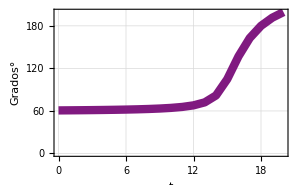

```mathematica
Tabla1=Table[{t, (θ1/.VartArt[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

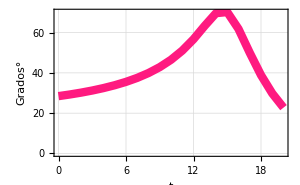

```mathematica
Tabla2=Table[{t, (θ2/.VartArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,1,.1,.5,"t", "Grados°"]
```

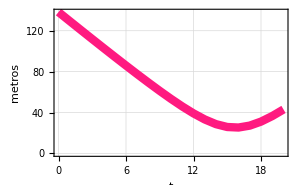

```mathematica
Tabla3=Table[{t, (d3/.VartArt[t])},{t,0,tf,1}];
Theta3=Grafica[Tabla3,1,.1,.5,"t", "metros"]
```

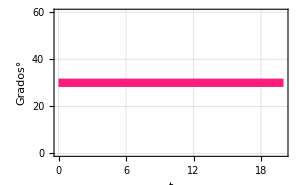

```mathematica
Tabla4=Table[{t, (θ4/.VartArt[t])/Degree},{t,0,tf,1}];
Theta4=Grafica[Tabla4,1,.1,.5,"t", "Grados°"]
```

```mathematica
Tabla5=Table[{t, (θ5/.VartArt[t])/Degree},{t,0,tf,1}];
Theta5=Grafica[Tabla5,1,.1,.5,"t", "Grados°"]
```

-Graphics-

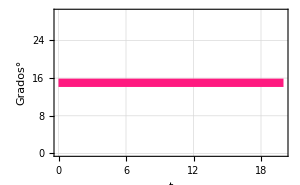

```mathematica
Tabla6=Table[{t, (θ6/.VartArt[t])/Degree},{t,0,tf,1}];
Theta6=Grafica[Tabla6,1,.1,.5,"t", "Grados°"]
```